Computes  ending angular error between the z-axis of a sphere of radius ri that starts at orientation {ψ0, θ0} where angle ψ0 is  from vertical, rotated θ0 about the world z-axis, after following a circular arc with radius rc centered at (rc*cos(alphac),rc*sin(alphac) with arc length phi1
Michael Williams (Yu Huang) and Aaron T. Becker

## Things to do: given a sphere with {ri,psi0_, theta0}, what is the maximum error caused by {rc,alphac,phi1} as phi1 varies? Can we always pick a {rc,alphac} that is does not increase angular error? What about the ratio of Δθ_final/Δψ_final? Can we make most of the change to θ and small changes to ψ as we make the circle smaller and smaller? If so, we can take a Taylor expansion for our proof.

```mathematica
ψfinal[ri_,rc_,alphac_,phi1_,psi0_, theta0_]:=ArcCos[(Cos[psi0] (ri^2+rc^2 Cos[(phi1 √(rc^2+ri^2))/ri]))/(rc^2+ri^2)+(rc (-1+Cos[(phi1 √(rc^2+ri^2))/ri]) (Cos[alphac]-Sin[alphac]))/(√(rc^2+ri^2))+(rc Sin[psi0] Sin[(phi1 √(rc^2+ri^2))/ri] Sin[alphac-theta0])/(√(rc^2+ri^2))]
```

```mathematica
(*Aaron's calculation:*)
ψfinalaaron[ri_,rc_,αc_, ψ1_,ψ0_,θ0_]:=ArcCos[(Cos[ψ0] (ri^2+rc^2 Cos[(√(rc^2+ri^2) ψ1)/ri])+rc Sin[ψ0] (-2 ri Cos[αc-θ0] Sin[(√(rc^2+ri^2) ψ1)/(2 ri)]^2+√(rc^2+ri^2) Sin[αc-θ0] Sin[(√(rc^2+ri^2) ψ1)/ri]))/(rc^2+ri^2)]
```

## Plot the error as a function of different variables

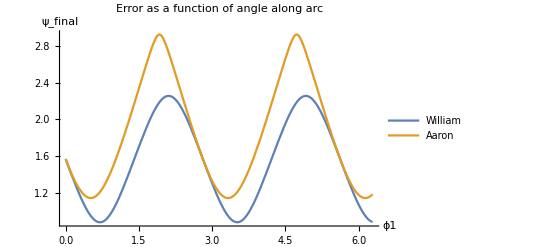

```mathematica
Plot[ {
ψfinal[1,2,45Degree,ϕ1,90Degree,0],
ψfinalaaron[1,2,45Degree,ϕ1,90Degree,0]},{ϕ1,0,2π},AxesLabel->{"ϕ1","ψ_final"},PlotLabel->"Error as a function of angle along arc",PlotLegends->{"William","Aaron"}]
```

Try this plot!

```mathematica
Manipulate[Plot[ {ψfinal[1,rc,45Degree,ϕ1,90Degree,225Degree],
ψfinalaaron[1,rc,45Degree,ϕ1,90Degree,225Degree]},{ϕ1,0,4π},AxesLabel->{"ϕ1","ψ_final, in Degrees"},PlotLabel->"Error as a function of angle along circular path",PlotRange->{Automatic,{0,π}},PlotLegends->{"William","Aaron"}],{rc,0.01,10}]
```

90 °-π

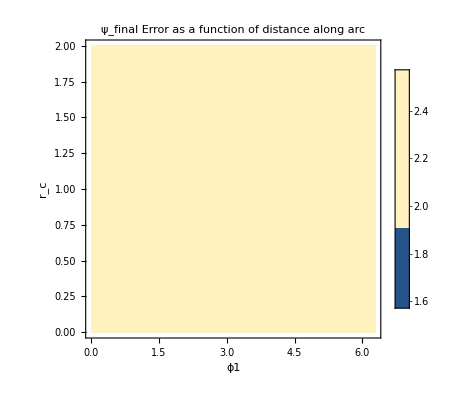

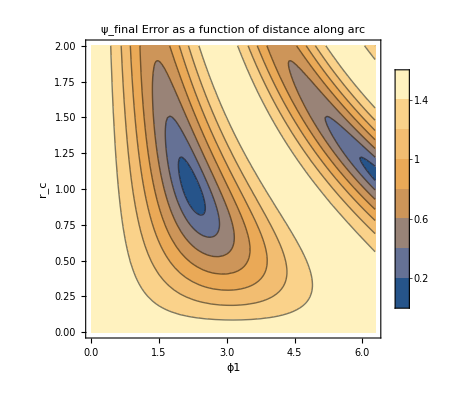

```mathematica
ψAt0 = 90Degree;
ContourPlot[ ψfinal[1,rc,45Degree,ϕ1,ψAt0,225Degree],{ϕ1,0,2π},{rc,0,2},FrameLabel->{"ϕ1","r_c"},PlotLabel->"ψ_final Error as a function of distance along arc",PlotLegends->Automatic]
ContourPlot[ ψfinalaaron[1,rc,45Degree,ϕ1,ψAt0,225Degree],{ϕ1,0,2π},{rc,0,2},FrameLabel->{"ϕ1","r_c"},PlotLabel->"ψ_final Error as a function of distance along arc",PlotLegends->Automatic]
```

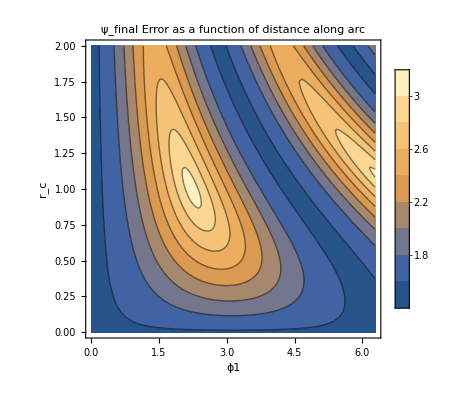

```mathematica
ContourPlot[ ψfinalaaron[1,rc,45Degree,ϕ1,ψAt0,45Degree],{ϕ1,0,2π},{rc,0,2},FrameLabel->{"ϕ1","r_c"},PlotLabel->"ψ_final Error as a function of distance along arc",PlotLegends->Automatic]
```

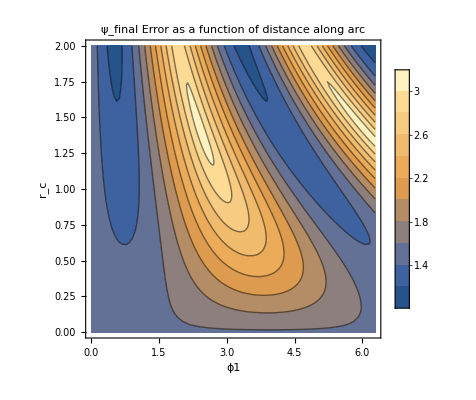

```mathematica
ContourPlot[ ψfinalaaron[1,rc,45Degree,ϕ1,ψAt0,0Degree],{ϕ1,0,2π},{rc,0,2},FrameLabel->{"ϕ1","r_c"},PlotLabel->"ψ_final Error as a function of distance along arc",PlotLegends->Automatic]
```

## Plot paths of the circle here I’d like to draw the sphere from a top down, and draw some paths and make the plane show the resulting error. This may be hard.

ri: the radius of the 1th ball.
rc: radius of the circle track.
alphac: I assume the ball`s initial position is on the origin of the word coordinates system and the center of the circle track is placed at (rc*cos(alphac),rc*sin(alphac))
psi0: initial psi value of the ball.
phi1: specify the arc length that the ball rolled along by giving the corresponding central angle of the arc.
theta0: initial theta value of the ball.

Sphere center at {0,0,ri}
Sphere rotates about {rc Cos[αc],rc Sin[αc],0}
Vector is {rc Cos[αc],rc Sin[αc],-ri}
Then the  ball rotatess about the lollipop stick -ϕ1  *rc/((ri*rc)/(√(ri^2+rc^2))) =-(√(rc^2+ri^2) ψ1)/ri

### Alternate Calculation

#### Calculate the angle the ball rotates about the lollipop stick. THe circle drawn on the sphere is of radius(ri*rc)/(√(ri^2+rc^2))

```mathematica
Clear[rc]
-ϕ1*rc/((ri*rc)/(√(ri^2+rc^2))) (*lollipop rotation angle*)
```

```mathematica
-(√(rc^2+ri^2) ϕ1)/ri
```

```mathematica
InitCond[ψ0_,θ0_]:=({{Sin[ψ0]Cos[θ0]}, {Sin[ψ0]Sin[θ0]}, {Cos[ψ0]}});
RotationMatrix[ϕ1,{0,0,1}]//MatrixForm  (*rotation about z-axis*)
Rot1 =Simplify[Refine[RotationMatrix[-(√(rc^2+ri^2) ϕ1)/ri,{rc Cos[αc],rc Sin[αc],-ri}],αc∈Reals&&ri∈Reals&&ri>0&&rc∈Reals&&rc>0]/.{Abs[Sin[αc]]->Sin[αc],Abs[Cos[αc]]->Cos[αc], Abs[Tan[αc]]-> Tan[αc]}];
```

(Cos[ϕ1] | -Sin[ϕ1] | 0
Sin[ϕ1] | Cos[ϕ1] | 0
0 | 0 | 1)

```mathematica
compositeRot=({{Cos[ϕ1], -Sin[ϕ1], 0}, {Sin[ϕ1], Cos[ϕ1], 0}, {0, 0, 1}}).Rot1.({{Sin[ψ0]Cos[θ0]}, {Sin[ψ0]Sin[θ0]}, {Cos[ψ0]}});
```

```mathematica
Simplify[ArcCos[compositeRot⟦3⟧]] (*grab 3rd element, the z-axis component, and acos[] of it*)
```

{ArcCos[1/(rc^2+ri^2)((ri^2+rc^2 Cos[(√(rc^2+ri^2) ϕ1)/ri]) Cos[ψ0]-rc (Sin[αc] (2 ri Sin[θ0] Sin[(√(rc^2+ri^2) ϕ1)/(2 ri)]^2-√(rc^2+ri^2) Cos[θ0] Sin[(√(rc^2+ri^2) ϕ1)/ri])+Cos[αc] (2 ri Cos[θ0] Sin[(√(rc^2+ri^2) ϕ1)/(2 ri)]^2+√(rc^2+ri^2) Sin[θ0] Sin[(√(rc^2+ri^2) ϕ1)/ri])) Sin[ψ0])]}

```mathematica
FullSimplify[ArcCos[1/(rc^2+ri^2)((ri^2+rc^2 Cos[(√(rc^2+ri^2) ϕ1)/ri]) Cos[ψ0]-rc (Sin[αc] (2 ri Sin[θ0] Sin[(√(rc^2+ri^2) ϕ1)/(2 ri)]^2-√(rc^2+ri^2) Cos[θ0] Sin[(√(rc^2+ri^2) ϕ1)/ri])+Cos[αc] (2 ri Cos[θ0] Sin[(√(rc^2+ri^2) ϕ1)/(2 ri)]^2+√(rc^2+ri^2) Sin[θ0] Sin[(√(rc^2+ri^2) ϕ1)/ri])) Sin[ψ0])]]
```

ArcCos[((ri^2+rc^2 Cos[(√(rc^2+ri^2) ϕ1)/ri]) Cos[ψ0]+rc (-2 ri Cos[αc-θ0] Sin[(√(rc^2+ri^2) ϕ1)/(2 ri)]^2+√(rc^2+ri^2) Sin[αc-θ0] Sin[(√(rc^2+ri^2) ϕ1)/ri]) Sin[ψ0])/(rc^2+ri^2)]

## The ψ angle doesn’t depend on the rotation about the z-axis

```mathematica
compEquivRot =Rot1 .({{Sin[ψ0]Cos[θ0]}, {Sin[ψ0]Sin[θ0]}, {Cos[ψ0]}});
Simplify[ArcCos[compEquivRot⟦3⟧]]
```

{ArcCos[1/(rc^2+ri^2)((ri^2+rc^2 Cos[(√(rc^2+ri^2) ϕ1)/ri]) Cos[ψ0]-rc (Sin[αc] (2 ri Sin[θ0] Sin[(√(rc^2+ri^2) ϕ1)/(2 ri)]^2-√(rc^2+ri^2) Cos[θ0] Sin[(√(rc^2+ri^2) ϕ1)/ri])+Cos[αc] (2 ri Cos[θ0] Sin[(√(rc^2+ri^2) ϕ1)/(2 ri)]^2+√(rc^2+ri^2) Sin[θ0] Sin[(√(rc^2+ri^2) ϕ1)/ri])) Sin[ψ0])]}

```mathematica
FullSimplify[ArcCos[1/(rc^2+ri^2)((ri^2+rc^2 Cos[(√(rc^2+ri^2) ϕ1)/ri]) Cos[ψ0]-rc (Sin[αc] (2 ri Sin[θ0] Sin[(√(rc^2+ri^2) ϕ1)/(2 ri)]^2-√(rc^2+ri^2) Cos[θ0] Sin[(√(rc^2+ri^2) ϕ1)/ri])+Cos[αc] (2 ri Cos[θ0] Sin[(√(rc^2+ri^2) ϕ1)/(2 ri)]^2+√(rc^2+ri^2) Sin[θ0] Sin[(√(rc^2+ri^2) ϕ1)/ri])) Sin[ψ0])]]
```

ArcCos[((ri^2+rc^2 Cos[(√(rc^2+ri^2) ϕ1)/ri]) Cos[ψ0]+rc (-2 ri Cos[αc-θ0] Sin[(√(rc^2+ri^2) ϕ1)/(2 ri)]^2+√(rc^2+ri^2) Sin[αc-θ0] Sin[(√(rc^2+ri^2) ϕ1)/ri]) Sin[ψ0])/(rc^2+ri^2)]

```mathematica
β=-(√(rc^2+ri^2) ϕ1)/ri
```

```mathematica
Simplify[ArcCos[(Cos[ψ0] (ri^2+rc^2 Cos[-β])+rc Sin[ψ0] (-2 ri Cos[αc-θ0] Sin[-β/2]^2+√(rc^2+ri^2) Sin[αc-θ0] Sin[-β]))/(rc^2+ri^2)]]
```

ArcCos[((ri^2+rc^2 Cos[β]) Cos[ψ0]-rc (2 ri Cos[αc-θ0] Sin[β/2]^2+√(rc^2+ri^2) Sin[β] Sin[αc-θ0]) Sin[ψ0])/(rc^2+ri^2)]